```mathematica
data1={{1982,3.52},{1983,2.64},{1984,2.19},{1985,3.85},{1986,4.06},{1987,3.62},{1989,3.66},{1992,3.4},{1993,3.09},{1994,3.22},{1996,3.26},{1997,2.48},{1998,2.03},{1999,2.51},{2002,3.64},{2003,4.4},{2004,3.94},{2006,3.03},{2007,3.27},{2009,3.42},{2010,2.89},{2011,3.11},{2012,3.22},{2014,3.8},{2015,3.7},{2016,3.58},{2017,4.58}};
tsm=TimeSeriesModelFit[data1,{"SARIMA",{{2,1,2},{4,0,2},5}}]
```

TemporalData::rsmplng: 数据没有均匀间隔，并且将自动采样到最小时间增量的解决方案 .

TimeSeriesModel[…]

```mathematica
Array[a,50,2018];
Array[b,50,2018];
Do[{a[n]=Part[tsm["PredictionLimits"][n],1],b[n]=Part[tsm["PredictionLimits"][n],2]},{n,2018,2067}]
u=Table[i*(2-j)+(j-1)*a[i],{i,2018,2067},{j,2}];
d=Table[i*(2-j)+(j-1)*b[i],{i,2018,2067},{j,2}];
```

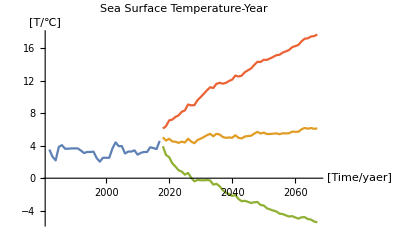

```mathematica
ListLinePlot[{tsm["TemporalData"],TimeSeriesForecast[tsm,{50}],u,d},AxesLabel->{RawBoxes[RowBox[{"[",RowBox[{"Time","/","yaer"}],"]"}]],RawBoxes[RowBox[{"[",RowBox[{"T","/","℃"}],"]"}]]},PlotLabel->HoldForm[Sea Surface Temperature-Year],LabelStyle->{FontFamily->"Times New Roman",12,GrayLevel[0]}]
```